# Quantum states of systems of chemical interest using NDEigensystem 11

Single sentence description of the topic

## Hamiltonian operator

Potential energy operator

```mathematica
𝒱[x__]:=-1/Norm[{x}]
```

Kinetic energy operator:

```mathematica
𝒦[ψ_][x__]:=-1/2∇_{x}^2 ψ[x]
```

Hamiltonian operator:

```mathematica
ℋ[ψ_][x__]:=𝒦[ψ][x]+𝒱[x]ψ[x]
```

#### Exercises:

Obtain the Hamiltonian for the Hydrogen atom in 1, 2, and 3 dimensions

Write the Schrodinger equation for the 1 dimensional Hydrogen atom.

## 1-Dimensional Hydrogen atom

### Analytical solutions for the 1 dimensional Hydrogen atom

Schrodinger equation for the 1 dimensional Hydrogen atom can be written as Kummer’s equation. The solutions of Kummer’s equation are the confluent hypergeometric functions Hypergeometric1F1[1-n,2, 2 x/n] .

Analytical solutions:

```mathematica
Subscript[f, n_][x_]:=x Exp[-x/n]Hypergeometric1F1[1-n,2, 2 x/n]
```

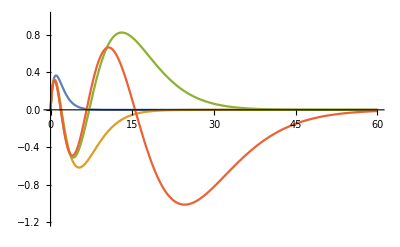

```mathematica
Plot[Evaluate@Table[Subscript[f, i][x],{i,1,4}],{x,0,60},PlotRange->{-1.2,1}]
```

In atomic units,the energies of the four lowest eigenstates are:

```mathematica
Subscript[ℰ, 1]=Table[N[-1/(2 i^2)],{i,1,4}]
```

{-0.5,-0.125,-0.0555556,-0.03125}

#### Exercises:

Are these functions normalized? If not, find the normalization constants for each eigenstate.

Define a normalized function.

#### Answer:

Find the normalization constant for each state:

```mathematica
nint=Table[NIntegrate[(Subscript[f, n][x])^2,{x,0,100}],{n,1,4}]
```

{0.25,2.,6.75,16.}

The normalization constant is

```mathematica
norm=1/Sqrt[nint]
```

{2.,0.707107,0.3849,0.25}

Normalization:

```mathematica
Subscript[Ψ, n_][x_]:=norm⟦n⟧ Subscript[f, n][x]
```

```mathematica
Table[NIntegrate[  Subscript[Ψ, i][x]^2,{x,0,100}],{i,1,4}]
```

{1.,1.,1.,1.}

### Boundary conditions

Physically the probability of finding the electron at x=0 should be zero. Computationally, the wave function should be zero at the end of the computational box. These requirements can be fulfilled using Dirichlet Boundary conditions.

Boundary conditions:

```mathematica
Subscript[ℬ, 1]=DirichletCondition[ψ[x]==0,True];
```

In atomic units, the energies of the four lowest eigenstates are:

### Eigensystem

The eigensystem is computed using a box of length ℓ and a discretization with interval Δx:

```mathematica
eigensystem[ℓ_,Δx_]:=
SortBy[
Transpose[
NDEigensystem[{ℋ[ψ][x],Subscript[ℬ, 1]},ψ,
{x,0,ℓ},50,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->Δx}}}}]],
First]
```

For Example:

```mathematica
NIntegrate[eigensystem[60,0.1][[4,2]][x]^2,{x,0,60}]
```

1.

#### Dynamic Programming

Consider dynamic programming and DumpSave for time consuming operations, e.g. replace

```mathematica
f[x_]:=x^2
```

by

```mathematica
f[x_]:=f[x]=x^2
```

```mathematica
Table[f[x],{x,0,5}]
```

{0,1,4,9,16,25}

and DumpSave the results

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Usuarios\94398430\Desktop\WSS_Project\WSS_project

```mathematica
DumpSave["myfile",f]
```

{f}

```mathematica
Clear[f]
```

```mathematica
<<myfile
```

```mathematica
f[3]
```

9

```mathematica
?f
```

Global`f

f[0]=0
 
f[1]=1
 
f[2]=4
 
f[3]=9
 
f[4]=16
 
f[5]=25
 
f[x_]:=f[x]=x^2

#### Normalisation

Verify that a given eigenstate is normalized:

```mathematica
{en,wf}=eigensystem[10,0.1]⟦2⟧
```

{-0.112806,InterpolatingFunction[{{0., 10.}}, <>]}

```mathematica
NIntegrate[wf[x]^2,{x,0,10}]
```

1.

#### Results for the 4 lowest energy eigenstates

```mathematica
Manipulate[
GraphicsGrid@
Partition[
(es↦Table[
Show[
Plot[{es⟦i,1⟧+(es⟦i,2⟧[x])^2,𝒱[x],Subscript[ℰ, 1]⟦i⟧+(Subscript[Ψ, i][x]^2)},{x,0,65},
PlotRange->{-0.6,0.1},
Filling->{1->es⟦i,1⟧,2-> Bottom,None}(*,
PlotLabel->label[i,es⟦i,1⟧,Subscript[ℰ, 1]⟦i⟧]*)]
],
{i,1,4}
])@
eigensystem[ℓ,Δx],
2],
{{ℓ,15,"Box Length"},2,62,5},
{{Δx,0.05,"Discretization"},0.1,0.01,-0.01}
]
```

#### Suggestions

Investigate Deployed→True for Manipulate

Use PaddedForm or NumberForm

```mathematica
NumberForm[0.34242523,{4,3}]//Text
```

0.342

```mathematica
PaddedForm[0.3,{4,3}]//Text
```

0.300

### Investigations

Use the sliding menus of the Manipulate to explore the solutions of NDEigensystem. Answer the following questions:

1) What factor is more important (ϵ, ℓ,Δx) for obtaining better eigenvalues?
2) What are the best values of the parameters (ϵ, ℓ,Δx) for the best possible match with the theoretical values?
3) How important is the regularization (parameter ϵ) for obtaining good match with the theoretical energies?

Repeat this pattern as needed to explain the section. Feel free to skip text lines if direction/caption lines are sufficient, but do not skip code cells.

## 2D-Hydrogen atom

The potential energy

```mathematica
Subscript[V, 2][x_,y_]:=-1/(√(x^2+y^2))
```

The Kinetic energy operator:

```mathematica
Subscript[K, 2][ψ_]:=-1/2∇_{x,y}^2 ψ
```

```mathematica
Subscript[K, 2][ψ[x,y]]
```

1/2 (-ψ^(0,2)[x,y]-ψ^(2,0)[x,y])

The Hamiltonian operator:

```mathematica
Subscript[ℋ, 2][ψ_]:=Subscript[K, 2][ψ]+Subscript[V, 2][x,y]ψ
```

The boundary conditions:

```mathematica
Subscript[ℬ, 2]=DirichletCondition[ψ[x,y]==0,True]
```

DirichletCondition[ψ[x,y]==0,True]

Now the region must be defined more carefully

```mathematica
Subscript[ℛ, 2]=Disk[{0,0},R]
```

Disk[{0,0},R]

In atomic units, the energies of the four lowest eigenstates are:

```mathematica
Subscript[ℰ, 2]=Subscript[ℰ, 1]
```

{-0.5,-0.125,-0.0555556,-0.03125}

```mathematica
Subscript[ℛ, 2]/.R->10
```

Disk[{0,0},10]

```mathematica
Subscript[ℋ, 2][ψ[x,y]]
```

-ψ[x,y]/(√(x^2+y^2))+1/2 (-ψ^(0,2)[x,y]-ψ^(2,0)[x,y])

```mathematica
temp=NDEigensystem[{Subscript[ℋ, 2][ψ[x,y]],Subscript[ℬ, 2]},ψ[x,y],{x,y}∈Subscript[ℛ, 2]/.R->10.,2,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}}}]
```

{{-0.0172593,-0.0313412},{InterpolatingFunction[{{-10., 10.}, {-10., 10.}}, <>][x,y],InterpolatingFunction[{{-10., 10.}, {-10., 10.}}, <>][x,y]}}

```mathematica
Plot3D[temp[[2,1]],{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
y
```

y

```mathematica
Plot3D[temp[[2,1]],{x,y}∈Evaluate[Subscript[ℛ, 2]/.R->10.]]
```

-Graphics3D-

Calculation of the 4 lowest energy eigenstates of the Hydrogen atom for different choices  of the calculation box ℓ, and the size of the spatial discretization Δx.

```mathematica
Manipulate[
Table[Plot3D[#⟦i,2⟧,{x,y}∈Evaluate[Subscript[ℛ, 2]/.R->rmax],PlotRange->All,PlotLabel->StringTemplate["E_(``) = `` (``)"][i,#⟦i,1⟧,Subscript[ℰ, 1]⟦i⟧]],{i,1,4}]&@SortBy[Transpose[NDEigensystem[{Subscript[ℋ, 2][ψ[x,y]],Subscript[ℬ, 2]},ψ[x,y],{x,y}∈Subscript[ℛ, 2]/.R-> rmax,40,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->Δx}}}}]],First],"R"->{rmax,2,62,10},"Δx"-> {Δx,0.1,0.01,-0.01}]
```

```mathematica
Laplacian[
```

## ns as needed to explain the topic (cmd/alt+4)

Section names, the total number of sections, and section organization will differ based on the topic.

Here are some ideas for sections you might consider:

history/origins
derivation
applications
common misunderstandings
recent developments
unanswered questions

Further Explorations

Name of a related topic for exploration

Name of another related topics for exploration (repeat as needed)

Authorship information

Name of Author

Date of creation

Author email address (please use the email associated with your Wolfram User ID)

PredictiveInterface`DoPredictionAction::newsess: Suggested actions are only available in the same kernel session that suggested them.